```mathematica
pivot[iStar_,jStar_,tab_]:=(
newTab=tab;
rows=Dimensions[tab][[1]];
cols=Dimensions[tab][[2]];
(* switch variables *)
newTab[[1,jStar]]=tab[[iStar,cols]];
newTab[[iStar,cols]]=tab[[1,jStar]];
For[ii=2,ii<=rows,ii++,
For[jj=1,jj<cols,jj++,
{
If[ii==iStar&&jj==jStar,newTab[[ii,jj]]=1/tab[[iStar,jStar]]];
If[ii==iStar&&jj!=jStar,newTab[[ii,jj]]=-tab[[ii,jj]]/tab[[iStar,jStar]]];
If[ii!=iStar&&jj==jStar,newTab[[ii,jj]]=tab[[ii,jj]]/tab[[iStar,jStar]]];
If[ii!=iStar&&jj!=jStar,newTab[[ii,jj]]=tab[[ii,jj]]-tab[[iStar,jj]]tab[[ii,jStar]]/tab[[iStar,jStar]]];
}
]
];
Return[newTab]
)
```

```mathematica
(* min z = −8x1​+10x2​−9
−2x1​−5x2​≥30
−2x1−2x2≥14
−x1−2x2≤28
−4x1​+5x2​≥−75
5x1+3x2≥−60
−3x1​+2x2​≤18
4x1−x2≤24
 *)
```

```mathematica
g1[x1_,x2_]:=-2x1-5x2;b1=30;
g2[x1_,x2_]:=-2x1-2x2;b2=14;
g3[x1_,x2_]:=-1x1-2x2;b3=28;
g4[x1_,x2_]:=-4x1+5x2;b4=-75;
g5[x1_,x2_]:=5x1+3x2;b5=-60;
g6[x1_,x2_]:=-3x1+2x2;b6=18;
g7[x1_,x2_]:=4x1-1x2;b7=24;

g1[x1_]=x2/.Solve[g1[x1,x2]==b1][[1,1]];
g2[x1_]=x2/.Solve[g2[x1,x2]==b2][[1,1]];
g3[x1_]=x2/.Solve[g3[x1,x2]==b3][[1,1]];
g4[x1_]=x2/.Solve[g4[x1,x2]==b4][[1,1]];
g5[x1_]=x2/.Solve[g5[x1,x2]==b5][[1,1]];
g6[x1_]=x2/.Solve[g6[x1,x2]==b6][[1,1]];
g7[x1_]=x2/.Solve[g7[x1,x2]==b7][[1,1]];
```

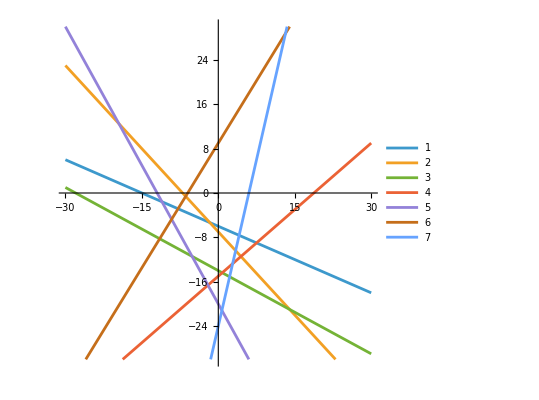

```mathematica
Plot[{g1[x],g2[x],g3[x],g4[x],g5[x], g6[x], g7[x]},{x,-30,30},PlotHighlighting->None,AspectRatio->Automatic,PlotRange->{-30,30},PlotLegends->Automatic]
```

```mathematica
a0={"u1","u2","u3","u4",1,""};
a1={-2,2,-5,5,-30,"s1"};
a2={-2,2,-2,2,-14,"s2"};
a3={1,-1,2,-2,28,"s3"};
a4={-4,4,5,-5,75,"s4"};
a5={5,-5, 3,-3, 60,"s5"};
a6={3,-3, -2,2, 18,"s6"};
a7={-4,4, 1,-1, 24,"s7"};
aObj={-8,8,10,-10,-9,"z"};
a={a0,a1,a2,a3,a4,a5,a6, a7, aObj};
Print["a = ",MatrixForm[a]]
```

a = (u1 | u2 | u3 | u4 | 1 | 
-2 | 2 | -5 | 5 | -30 | s1
-2 | 2 | -2 | 2 | -14 | s2
1 | -1 | 2 | -2 | 28 | s3
-4 | 4 | 5 | -5 | 75 | s4
5 | -5 | 3 | -3 | 60 | s5
3 | -3 | -2 | 2 | 18 | s6
-4 | 4 | 1 | -1 | 24 | s7
-8 | 8 | 10 | -10 | -9 | z)

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b]]
```

b = (u1 | s1 | u3 | u4 | 1 | 
1 | 1/2 | 5/2 | -5/2 | 15 | u2
0 | 1 | 3 | -3 | 16 | s2
0 | -1/2 | -1/2 | 1/2 | 13 | s3
0 | 2 | 15 | -15 | 135 | s4
0 | -5/2 | -19/2 | 19/2 | -15 | s5
0 | -3/2 | -19/2 | 19/2 | -27 | s6
0 | 2 | 11 | -11 | 84 | s7
0 | 4 | 30 | -30 | 111 | z)

```mathematica
c=pivot[3,4,b];
Print["c = ",MatrixForm[c]]
```

c = (u1 | s1 | u3 | s2 | 1 | 
1 | -1/3 | 0 | 5/6 | 5/3 | u2
0 | 1/3 | 1 | -1/3 | 16/3 | u4
0 | -1/3 | 0 | -1/6 | 47/3 | s3
0 | -3 | 0 | 5 | 55 | s4
0 | 2/3 | 0 | -19/6 | 107/3 | s5
0 | 5/3 | 0 | -19/6 | 71/3 | s6
0 | -5/3 | 0 | 11/3 | 76/3 | s7
0 | -6 | 0 | 10 | -49 | z)

```mathematica
d=pivot[2,2,c];
Print["d = ",MatrixForm[d]]
```

d = (u1 | u2 | u3 | s2 | 1 | 
3 | -3 | 0 | 5/2 | 5 | s1
1 | -1 | 1 | 1/2 | 7 | u4
-1 | 1 | 0 | -1 | 14 | s3
-9 | 9 | 0 | -5/2 | 40 | s4
2 | -2 | 0 | -3/2 | 39 | s5
5 | -5 | 0 | 1 | 32 | s6
-5 | 5 | 0 | -1/2 | 17 | s7
-18 | 18 | 0 | -5 | -79 | z)

```mathematica
e=pivot[8,1,d];
Print["e = ",MatrixForm[e]]
```

e = (s7 | u2 | u3 | s2 | 1 | 
-3/5 | 0 | 0 | 11/5 | 76/5 | s1
-1/5 | 0 | 1 | 2/5 | 52/5 | u4
1/5 | 0 | 0 | -9/10 | 53/5 | s3
9/5 | 0 | 0 | -8/5 | 47/5 | s4
-2/5 | 0 | 0 | -17/10 | 229/5 | s5
-1 | 0 | 0 | 1/2 | 49 | s6
-1/5 | 1 | 0 | -1/10 | 17/5 | u1
18/5 | 0 | 0 | -16/5 | -701/5 | z)

```mathematica
f=pivot[5,4,e];
Print["f = ",MatrixForm[f]]
```

f = (s7 | u2 | u3 | s4 | 1 | 
15/8 | 0 | 0 | -11/8 | 225/8 | s1
1/4 | 0 | 1 | -1/4 | 51/4 | u4
-13/16 | 0 | 0 | 9/16 | 85/16 | s3
9/8 | 0 | 0 | -5/8 | 47/8 | s2
-37/16 | 0 | 0 | 17/16 | 573/16 | s5
-7/16 | 0 | 0 | -5/16 | 831/16 | s6
-5/16 | 1 | 0 | 1/16 | 45/16 | u1
0 | 0 | 0 | 2 | -159 | z)

```mathematica
g=pivot[4,1,f];
Print["g = ",MatrixForm[g]]
```

g = (s3 | u2 | u3 | s4 | 1 | 
-30/13 | 0 | 0 | -1/13 | 525/13 | s1
-4/13 | 0 | 1 | -1/13 | 187/13 | u4
-16/13 | 0 | 0 | 9/13 | 85/13 | s7
-18/13 | 0 | 0 | 2/13 | 172/13 | s2
37/13 | 0 | 0 | -7/13 | 269/13 | s5
7/13 | 0 | 0 | -8/13 | 638/13 | s6
5/13 | 1 | 0 | -2/13 | 10/13 | u1
0 | 0 | 0 | 2 | -159 | z)